# Screening CMV vectors: Mathematical Foundations

## June 6, 2025

## Notation

The notation in this notebook differs slightly from that in the manuscript. Specifically, actively infected individuals are denoted by H rather than as I to avoid confusion with the symbol I used by Mathematica to denote an imaginary number.

## Population level model

The system of partial differential equations (PDEs) in the main text (1) reduces to the following system of ODEs if all model parameters are independent of age.

```mathematica
ODE={S'[t]->b (S[t]+L[t])+b(1-σ)H[t]-μ S[t]-α S[t]n[t]-β H[t] S[t],H'[t]->σ b H[t]+β H[t] S[t]+ρ L[t]-ω H[t]-μ H[t]-α H[t] n[t],L'[t]->ω H[t]-ρ L[t]-μ L[t]-α L[t] n[t]};
```

```mathematica
MatrixForm[ODE]
```

(S'[t]→b (1-σ) H[t]-μ S[t]-β H[t] S[t]-α n[t] S[t]+b (L[t]+S[t])
H'[t]→-μ H[t]+b σ H[t]-ω H[t]+ρ L[t]-α H[t] n[t]+β H[t] S[t]
L'[t]→ω H[t]-μ L[t]-ρ L[t]-α L[t] n[t])

## Steady-state solutions

### Find equilibria

```mathematica
EqSet=FullSimplify[Solve[{(S'[t]/.ODE/.{n[t]->S[t]+H[t]+L[t]})==0,(H'[t]/.ODE/.{n[t]->S[t]+H[t]+L[t]})==0,(L'[t]/.ODE/.{n[t]->S[t]+H[t]+L[t]})==0},{S[t],H[t],L[t]}]]
```

{{S[t]→0,H[t]→0,L[t]→0},{S[t]→(b-μ)/α,H[t]→0,L[t]→0},{S[t]→(b (b+ρ-(b+ρ) σ+ω))/(β (b+ρ)),H[t]→((b+ρ) (-β μ+b (β+α (-1+σ)))-b α ω)/(α β (b+ρ+ω)),L[t]→(ω ((b+ρ) (-β μ+b (β+α (-1+σ)))-b α ω))/(α β (b+ρ) (b+ρ+ω))},{S[t]→((μ+ρ) (μ-b σ)+μ ω)/(β (μ+ρ)),H[t]→(-μ+(b (μ+ρ) σ)/(μ+ρ+ω))/β,L[t]→(ω (-((μ+ρ) (μ-b σ))-μ ω))/(β (μ+ρ) (μ+ρ+ω))}}

Use “Reduce” to determine which of the two possible equilibrium solutions where the virus is present exists:

```mathematica
Reduce[(H[t]/.EqSet[[4]])>0&&β>0&&σ>=0&&σ<=1&&μ>0&&b>0&&α>0&&ω>=0&&ρ>=0,β]
```

α>0&&ρ≥0&&μ>0&&ω≥0&&0<σ≤1&&b>(μ^2+μ ρ+μ ω)/(μ σ+ρ σ)&&β>0

```mathematica
Reduce[(S[t]/.EqSet[[4]])>0&&β>0&&σ>=0&&σ<=1&&μ>0&&b>0&&α>0&&ω>=0&&ρ>=0,β]
```

(α>0&&ρ≥0&&μ>0&&ω≥0&&σ==0&&b>0&&β>0)||(α>0&&ρ≥0&&μ>0&&ω≥0&&0<σ≤1&&0<b<(μ^2+μ ρ+μ ω)/(μ σ+ρ σ)&&β>0)

Because the fourth equilibrium solution cannot have S and H positive simultaneously, we can rule it out. Numerical spot checks are consistent with this analysis:

```mathematica
EqSet[[4]]/.{b->11.1/365,μ->1/800,ω->1/21,ρ->1/31,β->.00001,σ->1/10}
```

{S[t]→-1.46934,H[t]→0.606884,L[t]→0.862456}

### Quantify prevalence at steady-state

We assume that only actively infected individuals in the H class shed virus and can be detected via sequencing of saliva samples. Thus, the prevalence of infection measured in the field is:

```mathematica
PrevAct=FullSimplify[(H[t]/(S[t]+H[t]+L[t]))/.EqSet[[3]],Assumptions->{β>0,μ>0,b>0,α>0,ω>=0,ρ>=0,b>μ,σ>=0,σ<=1}]
```

((b+ρ) (-β μ+b (β+α (-1+σ)))-b α ω)/(β (b-μ) (b+ρ+ω))

Although it cannot be directly measured in the field, the prevalence of latent infection at steady-state is:

```mathematica
PrevLat=FullSimplify[(L[t]/(S[t]+H[t]+L[t]))/.EqSet[[3]],Assumptions->{β>0,μ>0,b>0,α>0,ω>=0,ρ>=0,b>μ,σ>=0,σ<=1}]
```

(ω ((b+ρ) (-β μ+b (β+α (-1+σ)))-b α ω))/(β (b-μ) (b+ρ) (b+ρ+ω))

### Quantify force of infection at steady-state

```mathematica
SSF=FullSimplify[(β H[t])/.EqSet[[3]],Assumptions->{β>0,μ>0,b>0,α>0,ω>=0,ρ>=0,b>μ,σ>=0,σ<=1,n̂>0}]
```

((b+ρ) (-β μ+b (β+α (-1+σ)))-b α ω)/(α (b+ρ+ω))

Use this to define a replacement for β:

```mathematica
ToSSForce=Solve[λ==(b (b+ρ) (-1+σ)-b ω+β (b+ρ) n̂)/(b+ρ+ω),β]
```

{{β→(b^2+b λ+b ρ+λ ρ-b^2 σ-b ρ σ+b ω+λ ω)/((b+ρ) n̂)}}

### Define replacements/substitutions

At steady-state, the total population size is equal to:

```mathematica
RepSteadyN={n[t]->(b-μ)/α};
```

At steady-state, α is equal to :

```mathematica
RepAlpha={α->(b-μ)/(n̂)};
```

where n̂ is the steady-state population size.

## Calculate R_0

We calculate R_0 as a convenient tool for simplifying expressions

Define the Jacobian:

```mathematica
Jac=Grad[{(S'[t]/.ODE/.RepSteadyN),(H'[t]/.ODE/.RepSteadyN),(L'[t]/.ODE/.RepSteadyN)},{S[t],H[t],L[t]}]
```

{{-β H[t],b (1-σ)-β S[t],b},{β H[t],-b+b σ-ω+β S[t],ρ},{0,ω,-b-ρ}}

Calculate eigenvalues:

```mathematica
ESet=FullSimplify[Eigenvalues[Jac/.EqSet[[2]]]/.RepAlpha]
```

{0,1/2 (-ρ+b (-2+σ)-ω)-(n̂ (-b β+β μ+√(((b-μ)^2 ((ρ+b σ)^2+2 (ρ-b σ) ω+ω^2+β n̂ (2 ρ+2 b σ-2 ω+β n̂)))/(n̂)^2)))/(2 (b-μ)),1/2 (-ρ+b (-2+σ)-ω)+(n̂ (b β-β μ+√(((b-μ)^2 ((ρ+b σ)^2+2 (ρ-b σ) ω+ω^2+β n̂ (2 ρ+2 b σ-2 ω+β n̂)))/(n̂)^2)))/(2 (b-μ))}

Identify conditions required for the leading eigenvalue to be positive:

```mathematica
Reduce[ESet[[2]]>0&&β>0&&b>0&&μ>0&&ρ>0&&ω>0&&n̂>0&&b>μ]
```

False

```mathematica
Reduce[ESet[[3]]>0&&β>0&&b>0&&μ>0&&ρ>0&&ω>0&&n̂>0&&b>μ,β]
```

ρ>0&&b>0&&ω>0&&((σ<(b+ρ+ω)/(b+ρ)&&0<μ<b&&n̂>0&&β>(b^2+b ρ-b^2 σ-b ρ σ+b ω)/(b n̂+ρ n̂))||(σ≥(b+ρ+ω)/(b+ρ)&&0<μ<b&&n̂>0&&β>0))

This implies that R_0 is:

```mathematica
CheckR0=FullSimplify[(β(b n̂+ρ n̂))/(b^2+b ρ-b^2 σ-b ρ σ+b ω)]
```

-(β (b+ρ) n̂)/(b (b+ρ) (-1+σ)-b ω)

Rewrite and check

```mathematica
FullSimplify[-(β (b+ρ) n̂)/(b (b+ρ) (-1+σ)-b ω)==(β (b+ρ) n̂)/(b (b+ρ) (1-σ)+b ω)]
```

True

Define a replacement rule for β in terms of R_0

```mathematica
RepR0={β->R0 (b (b+ρ) (1-σ)+b ω)/((b+ρ) n̂)};
```

## Rewrite expressions in simplified forms

The force of infection at steady state is:

```mathematica
SSF
```

((b+ρ) (-β μ+b (β+α (-1+σ)))-b α ω)/(α (b+ρ+ω))

Which can be simplified by re-writing in terms of R_0 and replacing α with its steady state value:

```mathematica
ForC=FullSimplify[SSF/.RepR0/.RepAlpha,Assumptions->{R0>1,μ>0,b>0,α>0,ω>=0,ρ>=0,b>μ,σ>=0,σ<=1,n̂>0,b>μ}]
```

(b (-1+R0) (b+ρ-(b+ρ) σ+ω))/(b+ρ+ω)

This can be re-written as:

```mathematica
FullSimplify[(b (R0-1) ((b+ρ) (1-σ)+ω))/(b+ρ+ω)==ForC]
```

True

Send this to CForm so that it can be used in the likelihood calculations implemented in C++

```mathematica
CForm[ForC/.{ρ->rho,β->beta,ω->omega,σ->sigma,n̂->nhat}]
```

(b*(-1 + R0)*(b + omega + rho - (b + rho)*sigma))/(b + omega + rho)

## Individual-level model

When the population as a whole is at steady-state, we can study the probability that an individual animal is in each model state as a function of its age, a, using the following system of ODEs:

```mathematica
IODE={s'[a]->- λ s[a],h'[a]->λ s[a]+ρ l[a]-ω h[a],l'[a]->ω h[a]-ρ l[a]};
```

where λ is the force of infection at steady-state calculated previously. This works because when the population as a whole is at steady-state, the force of infection is constant and experienced identically by all animals within the population.

```mathematica
MatrixForm[IODE]
```

(s'[a]→-λ s[a]
h'[a]→-ω h[a]+ρ l[a]+λ s[a]
l'[a]→ω h[a]-ρ l[a])

Conveniently, this system of ODEs can be solved directly:

```mathematica
ISolGeneric=FullSimplify[FullSimplify[DSolve[{s'[a]==(s'[a]/.IODE),h'[a]==(h'[a]/.IODE),l'[a]==(l'[a]/.IODE),s[0]==so,h[0]==ho,l[0]==0},{s[a],h[a],l[a]},a,Assumptions->λ>0&&σ>=0&&σ<=1ρ>=0&&ω>=0&&a>0]]/.{ho+so->1}]
```

{{h[a]→(ⅇ^(-a λ) (so (λ-ρ) (ρ+ω)+ⅇ^(a λ) ρ (-λ+ρ+ω)+ⅇ^(a (λ-ρ-ω)) ω (-so λ+ho (-λ+ρ+ω))))/((ρ+ω) (-λ+ρ+ω)),l[a]→(ⅇ^(-a λ) ω (ⅇ^(a (λ-ρ-ω)) (so λ+ho (λ-ρ-ω))-so (ρ+ω)+ⅇ^(a λ) (-λ+ρ+ω)))/((ρ+ω) (-λ+ρ+ω)),s[a]→ⅇ^(-a λ) so}}

To complete our solution, we need to specify initial conditions. Assuming steady-state, we know that the probability an animal of age zero is in the susceptible state is:

```mathematica
SSso=FullSimplify[(1-σ H[t]/(S[t]+H[t]+L[t]))/.EqSet[[3]]/.ToSSForce/.RepSteadyN/.RepAlpha][[1]]
```

((b+λ) ((b+ρ) (-1+σ)-ω))/((b+ρ) (-λ+b (-1+σ))-(b+λ) ω)

and that the probability an animal of age zero is in the actively infected state is:

```mathematica
SSho=FullSimplify[ σ H[t]/(S[t]+H[t]+L[t])/.EqSet[[3]]/.ToSSForce/.RepSteadyN/.RepAlpha][[1]]
```

(λ (b+ρ) σ)/((b+ρ) (b+λ-b σ)+(b+λ) ω)

Stupidity check:

```mathematica
FullSimplify[SSso+SSho]
```

1

Find the final solution using the initial conditions:

```mathematica
ISol=FullSimplify[ISolGeneric/.{so->SSso,ho->SSho}]
```

{{h[a]→(ⅇ^(-a λ) (ⅇ^(a λ) ρ (-λ+ρ+ω)+((b+λ) (λ-ρ) ((b+ρ) (-1+σ)-ω) (ρ+ω))/((b+ρ) (-λ+b (-1+σ))-(b+λ) ω)-(ⅇ^(a (λ-ρ-ω)) λ (b+λ-(b+ρ) σ) ω (b+ρ+ω))/((b+ρ) (b+λ-b σ)+(b+λ) ω)))/((ρ+ω) (-λ+ρ+ω)),l[a]→(ⅇ^(-a λ) ω (ⅇ^(a λ) (-λ+ρ+ω)-((b+λ) ((b+ρ) (-1+σ)-ω) (ρ+ω))/((b+ρ) (-λ+b (-1+σ))-(b+λ) ω)+(ⅇ^(a (λ-ρ-ω)) λ (b+λ-(b+ρ) σ) (b+ρ+ω))/((b+ρ) (b+λ-b σ)+(b+λ) ω)))/((ρ+ω) (-λ+ρ+ω)),s[a]→(ⅇ^(-a λ) (b+λ) (b+ρ-(b+ρ) σ+ω))/((b+ρ) (b+λ-b σ)+(b+λ) ω)}}

## Define the Likelihood

This is the Log probability of observing a masCMV positive animal:

```mathematica
FPos=Expand[FullSimplify[Log[h[a]/.ISol]][[1]]]
```

Log[(ⅇ^(-a λ) (ⅇ^(a λ) ρ (-λ+ρ+ω)+((b+λ) (λ-ρ) ((b+ρ) (-1+σ)-ω) (ρ+ω))/((b+ρ) (-λ+b (-1+σ))-(b+λ) ω)-(ⅇ^(a (λ-ρ-ω)) λ (b+λ-(b+ρ) σ) ω (b+ρ+ω))/((b+ρ) (b+λ-b σ)+(b+λ) ω)))/((ρ+ω) (-λ+ρ+ω))]

This is the Log probability of observing a masCMV negative animal:

```mathematica
FNeg=Expand[FullSimplify[Log[(1-h[a])/.ISol]][[1]]]
```

Log[1-(ⅇ^(-a λ) (ⅇ^(a λ) ρ (-λ+ρ+ω)+((b+λ) (λ-ρ) ((b+ρ) (-1+σ)-ω) (ρ+ω))/((b+ρ) (-λ+b (-1+σ))-(b+λ) ω)-(ⅇ^(a (λ-ρ-ω)) λ (b+λ-(b+ρ) σ) ω (b+ρ+ω))/((b+ρ) (b+λ-b σ)+(b+λ) ω)))/((ρ+ω) (-λ+ρ+ω))]

```mathematica
CForm[FPos/.{ρ->rho,β->beta,ω->omega,σ->sigma,n̂->nhat,λ->Force}]
```

Log((Power(E,a*Force)*rho*(-Force + omega + rho) + 
      ((b + Force)*(Force - rho)*(omega + rho)*(-omega + (b + rho)*(-1 + sigma)))/
       (-((b + Force)*omega) + (b + rho)*(-Force + b*(-1 + sigma))) - 
      (Power(E,a*(Force - omega - rho))*Force*omega*(b + omega + rho)*
         (b + Force - (b + rho)*sigma))/((b + Force)*omega + (b + rho)*(b + Force - b*sigma)))/
    (Power(E,a*Force)*(omega + rho)*(-Force + omega + rho)))

```mathematica
CForm[FNeg/.{ρ->rho,β->beta,ω->omega,σ->sigma,n̂->nhat,λ->Force}]
```

Log(1 - (Power(E,a*Force)*rho*(-Force + omega + rho) + 
       ((b + Force)*(Force - rho)*(omega + rho)*(-omega + (b + rho)*(-1 + sigma)))/
        (-((b + Force)*omega) + (b + rho)*(-Force + b*(-1 + sigma))) - 
       (Power(E,a*(Force - omega - rho))*Force*omega*(b + omega + rho)*
          (b + Force - (b + rho)*sigma))/((b + Force)*omega + (b + rho)*(b + Force - b*sigma)))/
     (Power(E,a*Force)*(omega + rho)*(-Force + omega + rho)))

## Simulate Data Sets

This section simulates data sets that are used to test the parameter estimation procedure. These simulated data sets are output as a individual data files with numerical indices. The C++ code is set up (as an option) to read in numerically indexed data files and perform inference on each in turn.

### Define functions required for simulation

These functions are all derived above but are hard-coded here as well so that this section can be run independently if desired.

The probability that an individual of age a is actively infected:

```mathematica
PAct=(ⅇ^(-a λ) (ⅇ^(a λ) ρ (-λ+ρ+ω)+((b+λ) (λ-ρ) ((b+ρ) (-1+σ)-ω) (ρ+ω))/((b+ρ) (-λ+b (-1+σ))-(b+λ) ω)-(ⅇ^(a (λ-ρ-ω)) λ (b+λ-(b+ρ) σ) ω (b+ρ+ω))/((b+ρ) (b+λ-b σ)+(b+λ) ω)))/((ρ+ω) (-λ+ρ+ω));
```

The force of infection at steady state:

```mathematica
RepLambda={λ->(b (b+ρ) (-1+σ)-b ω+β (b+ρ) n̂)/(b+ρ+ω)};
```

A replacement for transmission rate that re-writes the model in terms of R_0:

```mathematica
RepR0={β->R0 (b (b+ρ) (1-σ)+b ω)/((b+ρ) n̂)};
```

### Multi-data set simulator with randomly drawn parameters

Sample size is set to 228 as in the real data and we assume only post-weaning animals older than 21 are sampled. Parameters are drawn at random from distributions selected to span the range of the biologically plausible for the Mastomys natalensis CMV system as described in the manuscript.

```mathematica
SampleSize=228;
```

```mathematica
MinAge=21;
```

```mathematica
DataSets=100;
```

```mathematica
Module[{i,j},ParmList={};ParmList=Append[ParmList,{"replicate","b","R0","omega","rho","sigma"}];For[i=0,i<DataSets,i++,Ages={};Parms={b->RandomReal[{1/200,1/700}],R0->RandomReal[{2,10}],ω->RandomReal[{0,1/21}],ρ->RandomReal[{0,1/21}],σ->RandomReal[{0,0.2}]};ParmList=Append[ParmList,{i,b/.Parms,R0/.Parms,ω/.Parms,ρ/.Parms,σ/.Parms}];
While[Length[Ages]<SampleSize,TryMe=RandomReal[ExponentialDistribution[b/.Parms]];If[TryMe>MinAge,Ages=Append[Ages,TryMe]]];
States=Table[{Ages[[i]],RandomInteger[BernoulliDistribution[PAct/.a->Ages[[i]]/.RepLambda/.RepR0/.Parms]]},{i,1,Length[Ages]}];Export["/home/scott-nuismer/Work/Current_Projects/Analyses of SL Field Data CMV/CPP_Code/MySimulatedData"<>ToString[i]<>".csv",States]];Export["/home/scott-nuismer/Work/Current_Projects/Analyses of SL Field Data CMV/CPP_Code/MySimulatedParms.csv",ParmList]]
```

/home/scott-nuismer/Work/Current_Projects/Analyses of SL Field Data CMV/CPP_Code/MySimulatedParms.csv

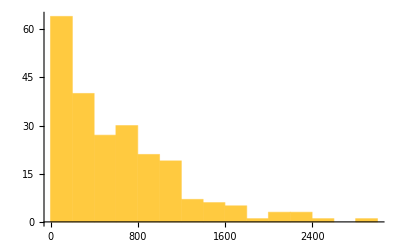

```mathematica
Histogram[Ages]
```

```mathematica
MatrixForm[ParmList]
```

(replicate | b | R0 | omega | rho | sigma
0 | 0.00381621 | 6.93276 | 0.0286127 | 0.0382602 | 0.184879
1 | 0.00399996 | 2.6686 | 0.0039179 | 0.0153194 | 0.143699
2 | 0.00274983 | 4.3298 | 0.0163555 | 0.0331046 | 0.195097
3 | 0.00468145 | 6.70025 | 0.00556621 | 0.0156477 | 0.0413836
4 | 0.00234009 | 7.91769 | 0.0373642 | 0.0294919 | 0.0749661
5 | 0.00339129 | 3.54854 | 0.0291448 | 0.0453148 | 0.113942
6 | 0.00179332 | 9.88524 | 0.0330847 | 0.0139049 | 0.118784
7 | 0.00256397 | 2.62953 | 0.0410713 | 0.020618 | 0.144324
8 | 0.00176013 | 6.52605 | 0.0389568 | 0.00486076 | 0.174963
9 | 0.00186116 | 7.79604 | 0.0180588 | 0.00565233 | 0.0583575
10 | 0.00303426 | 3.67789 | 0.0140114 | 0.0222939 | 0.0567379
11 | 0.00384911 | 9.46134 | 0.0339408 | 0.0340704 | 0.141739
12 | 0.00350953 | 8.56529 | 0.022083 | 0.0302949 | 0.134429
13 | 0.004388 | 7.11551 | 0.0187005 | 0.0374419 | 0.152999
14 | 0.00257153 | 5.49754 | 0.0400052 | 0.00681816 | 0.0133362
15 | 0.00203406 | 7.01038 | 0.00898473 | 0.018476 | 0.100551
16 | 0.00422288 | 6.26831 | 0.013308 | 0.025957 | 0.134016
17 | 0.00378045 | 2.38302 | 0.0407808 | 0.0145178 | 0.0177206
18 | 0.00332062 | 2.96216 | 0.0458498 | 0.00402463 | 0.123593
19 | 0.00480692 | 3.22122 | 0.00925201 | 0.00308368 | 0.181837
20 | 0.00460681 | 6.82022 | 0.0195595 | 0.0153638 | 0.17575
21 | 0.00208776 | 4.18093 | 0.0343047 | 0.0158102 | 0.0313444
22 | 0.0038391 | 5.87455 | 0.017125 | 0.0167704 | 0.116682
23 | 0.00257135 | 6.47383 | 0.0019354 | 0.0376487 | 0.182414
24 | 0.00268093 | 9.23015 | 0.00851975 | 0.0376383 | 0.179084
25 | 0.00319937 | 4.91397 | 0.00724018 | 0.041104 | 0.104734
26 | 0.00490304 | 9.77899 | 0.0249947 | 0.0160332 | 0.0434127
27 | 0.00143056 | 7.68812 | 0.0431815 | 0.0406119 | 0.173584
28 | 0.00446285 | 3.0828 | 0.0329714 | 0.0172379 | 0.094463
29 | 0.00303008 | 3.85739 | 0.000106816 | 0.0428274 | 0.0236345
30 | 0.00333073 | 3.448 | 0.019489 | 0.0194816 | 0.0537418
31 | 0.00252037 | 3.64122 | 0.0469461 | 0.0143949 | 0.145952
32 | 0.00147378 | 2.57586 | 0.0190834 | 0.0029944 | 0.163842
33 | 0.00471473 | 6.78028 | 0.00690903 | 0.0421872 | 0.126531
34 | 0.00453786 | 9.54939 | 0.0199287 | 0.0132728 | 0.101828
35 | 0.00147632 | 8.43931 | 0.00812829 | 0.0265154 | 0.145392
36 | 0.00220138 | 2.26439 | 0.0195108 | 0.0201616 | 0.0986605
37 | 0.00155397 | 8.62262 | 0.00788374 | 0.015956 | 0.191702
38 | 0.00486886 | 9.24825 | 0.0154866 | 0.0165825 | 0.14225
39 | 0.00279728 | 2.3914 | 0.00978828 | 0.00365236 | 0.193124
40 | 0.0031056 | 6.8862 | 0.0177818 | 0.0399156 | 0.187285
41 | 0.00147296 | 2.16109 | 0.00440883 | 0.00998121 | 0.0517981
42 | 0.00447965 | 3.64203 | 0.00367191 | 0.00787969 | 0.162841
43 | 0.0043662 | 9.62275 | 0.00820734 | 0.0021326 | 0.0527449
44 | 0.00252248 | 8.26817 | 0.0450327 | 0.0450122 | 0.057527
45 | 0.00250926 | 2.93843 | 0.0422757 | 0.0406479 | 0.117138
46 | 0.00337226 | 3.12078 | 0.00358347 | 0.00431542 | 0.153029
47 | 0.00163545 | 5.2 | 0.0264671 | 0.0207976 | 0.170347
48 | 0.00158635 | 7.4919 | 0.0387819 | 0.0134278 | 0.0391339
49 | 0.00295434 | 6.55749 | 0.0279194 | 0.0102764 | 0.0152983
50 | 0.00231427 | 5.14291 | 0.00375677 | 0.0412425 | 0.0283755
51 | 0.00482215 | 6.64314 | 0.00921495 | 0.0278943 | 0.0655176
52 | 0.00433035 | 7.86231 | 0.0222917 | 0.0390829 | 0.0840463
53 | 0.0034951 | 9.71547 | 0.037705 | 0.0402797 | 0.101744
54 | 0.00262029 | 9.32486 | 0.0374914 | 0.0150665 | 0.10184
55 | 0.00190147 | 5.24018 | 0.0119728 | 0.0144739 | 0.0480463
56 | 0.00442167 | 7.01165 | 0.0391812 | 0.0308423 | 0.0247917
57 | 0.00262519 | 5.89004 | 0.02921 | 0.0102475 | 0.0506125
58 | 0.00286011 | 5.3421 | 0.015367 | 0.0254637 | 0.0377481
59 | 0.00371395 | 7.60286 | 0.0340332 | 0.0307046 | 0.196066
60 | 0.00164559 | 6.54261 | 0.0330094 | 0.0134315 | 0.0315602
61 | 0.00413742 | 6.48486 | 0.0382365 | 0.0292152 | 0.144074
62 | 0.00253048 | 7.73812 | 0.0391124 | 0.04291 | 0.165079
63 | 0.00282064 | 2.10419 | 0.00459784 | 0.0197876 | 0.0244523
64 | 0.00290206 | 9.94584 | 0.0253588 | 0.00704192 | 0.110534
65 | 0.00351076 | 2.37981 | 0.0440456 | 0.016355 | 0.0336176
66 | 0.00269876 | 7.5039 | 0.0243071 | 0.0404635 | 0.138558
67 | 0.00338073 | 9.84003 | 0.00564347 | 0.037027 | 0.0370335
68 | 0.00409798 | 8.0412 | 0.0251372 | 0.0263682 | 0.178602
69 | 0.00306704 | 8.24158 | 0.0191155 | 0.0136628 | 0.055944
70 | 0.00265426 | 8.91744 | 0.0213948 | 0.021832 | 0.102854
71 | 0.00300245 | 7.66511 | 0.00756938 | 0.0423835 | 0.0237689
72 | 0.00260908 | 3.684 | 0.00501918 | 0.0316198 | 0.0106833
73 | 0.00158208 | 4.95371 | 0.00569827 | 0.0169249 | 0.111798
74 | 0.00472837 | 5.27999 | 0.0423765 | 0.0086632 | 0.165068
75 | 0.00394869 | 7.19381 | 0.0276852 | 0.0203556 | 0.025155
76 | 0.00233849 | 7.59575 | 0.0214401 | 0.00881264 | 0.0899527
77 | 0.00443422 | 8.02066 | 0.00431668 | 0.0415817 | 0.161724
78 | 0.00492455 | 3.33197 | 0.0124016 | 0.0127481 | 0.179864
79 | 0.00155108 | 9.28848 | 0.0415781 | 0.0276082 | 0.0223872
80 | 0.00476844 | 8.77824 | 0.00165469 | 0.0374733 | 0.0544757
81 | 0.00170663 | 5.97451 | 0.00546866 | 0.0154161 | 0.136386
82 | 0.00336481 | 9.19723 | 0.0324822 | 0.00618141 | 0.155767
83 | 0.00359782 | 8.86805 | 0.00367152 | 0.026924 | 0.163947
84 | 0.00285571 | 2.4317 | 0.0297647 | 0.0319844 | 0.0666137
85 | 0.00363111 | 5.04928 | 0.00543672 | 0.0398915 | 0.0255748
86 | 0.00188911 | 3.94644 | 0.0209089 | 0.0458725 | 0.106411
87 | 0.00237749 | 4.75035 | 0.0320053 | 0.00291157 | 0.0623402
88 | 0.00449121 | 8.61001 | 0.00119243 | 0.0333498 | 0.168304
89 | 0.00405296 | 7.86954 | 0.0452026 | 0.0223395 | 0.0532612
90 | 0.00358726 | 7.41871 | 0.0456635 | 0.0049208 | 0.184137
91 | 0.00444515 | 9.74358 | 0.0435976 | 0.0141786 | 0.0421031
92 | 0.00293656 | 7.39676 | 0.0449498 | 0.0378641 | 0.0967827
93 | 0.00238157 | 4.2747 | 0.00619399 | 0.024853 | 0.178002
94 | 0.00382793 | 2.01413 | 0.00356396 | 0.00543838 | 0.107566
95 | 0.00399993 | 8.28162 | 0.0205375 | 0.0309812 | 0.163418
96 | 0.00424013 | 5.40189 | 0.0129485 | 0.00735585 | 0.134984
97 | 0.00344607 | 3.38704 | 0.00881685 | 0.038824 | 0.0849337
98 | 0.00377923 | 5.73567 | 0.0362549 | 0.00252082 | 0.162714
99 | 0.00171615 | 2.61202 | 0.0457973 | 0.035568 | 0.00429385)

```mathematica
Length[States]
```

228

## Derivation of probability of being in active vs. latent state

Assuming an individual is infected at time 0, what is the probability it is in the actively infected vs latent state as time progresses? What is its asymptotic probability of being in each state?

```mathematica
WhichState=FullSimplify[DSolve[{x'[t]==-ω x[t]+ρ y[t],y'[t]==ω x[t]-ρ y[t],x[0]==0,y[0]==1},{x[t],y[t]},t]]
```

{{x[t]→(ρ-ⅇ^(-t (ρ+ω)) ρ)/(ρ+ω),y[t]→(ⅇ^(-t (ρ+ω)) ρ+ω)/(ρ+ω)}}

```mathematica
Limit[x[t]/.WhichState,t->∞]
```

{ConditionalExpression[ρ/(ρ+ω), ρ+ω>0]}

```mathematica
Limit[y[t]/.WhichState,t->∞]
```

{ConditionalExpression[ω/(ρ+ω), ρ+ω>0]}

Thus, the probability an infected individual is actively shedding and detectable is given by:

```mathematica
PropShed=ρ/(ρ+ω);
```